## 3.029 Spring 2022 Lecture 07 - 02/22/2022

## Thermodynamic Stability

Last week we talked about the fundamental thermodynamic relation

and used is in conjunction with the Legendre transform to introduce various other thermodynamic potentials

In-fact, the “natural” variables we defined for each of the thermodynamic potentials are chosen such that they minimize the thermodynamic potential

E.g. the Euler equation  is minimized for particular values of  and

## Minimum Conditions

For a function to be at a minimum:

Its first derivative must vanish

Its second derivative must be positive

```mathematica
univariateFunction[x_]=2 x^4-10 x^2+7x
```

7 x-10 x^2+2 x^4

```mathematica
univariateMinimaSols=Solve[{
univariateFunction'[x]==0,
univariateFunction''[x]>0
},x]//N
```

{{x→-1.73343},{x→1.36312}}

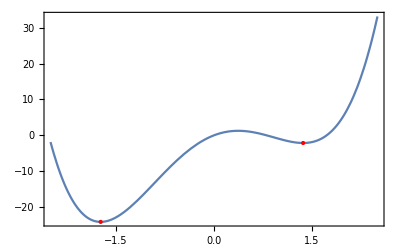

```mathematica
Plot[univariateFunction[x],{x,-5/2,5/2},Epilog->{Red,PointSize[Large],Point[{x,univariateFunction[x]}/.univariateMinimaSols]},Frame->True]
```

Note this a local minimum test

In contrast `Minimize` returns the global minimum

```mathematica
Minimize[univariateFunction[x],x]//N
```

{-24.1244,{x→-1.73343}}

For multivariate functions, a similar idea exists. 
E.g. for functions of two variables

∇_{x,y} f[x,y]={0,0}

The Hessian has to be positive-semi definite

I.e. it has non-negative eigenvalues

```mathematica
hessian[f_,vars_]:=Grad[Grad[f@@vars,vars],vars]
```

```mathematica
MatrixForm[hessian[f,{x,y,z}]]
```

(f^(2,0,0)[x,y,z] | f^(1,1,0)[x,y,z] | f^(1,0,1)[x,y,z]
f^(1,1,0)[x,y,z] | f^(0,2,0)[x,y,z] | f^(0,1,1)[x,y,z]
f^(1,0,1)[x,y,z] | f^(0,1,1)[x,y,z] | f^(0,0,2)[x,y,z])

```mathematica
multivariateFunction[x_,y_]=2 x^4-10 x^2+7x y+5 y^2
```

-10 x^2+2 x^4+7 x y+5 y^2

```mathematica
Thread[{a,b,c}=={1,2,3,4}]
```

False

```mathematica
Grad[multivariateFunction[x,y],{x,y}]
```

{-20 x+8 x^3+7 y,7 x+10 y}

```mathematica
Thread[Grad[multivariateFunction[x,y],{x,y}]==0]
```

{-20 x+8 x^3+7 y==0,7 x+10 y==0}

```mathematica
D[multivariateFunction[x,y],y,y]
```

10

```mathematica
MatrixForm[hessian[multivariateFunction,{x,y}]]
```

(-20+24 x^2 | 7
7 | 10)

```mathematica
hessian[multivariateFunction,{x,y}]
```

{{-20+24 x^2,7},{7,10}}

```mathematica
Thread[Eigenvalues[hessian[multivariateFunction,{x,y}]]>0]
```

{-5+12 x^2-√2 √(137-180 x^2+72 x^4)>0,-5+12 x^2+√2 √(137-180 x^2+72 x^4)>0}

```mathematica
multivariateMinimaSols=Solve[
Join[
Thread[Grad[multivariateFunction[x,y],{x,y}]==0],
Thread[Eigenvalues[hessian[multivariateFunction,{x,y}]]>0]
],{x,y}]//N
```

{{x→-1.76423,y→1.23496},{x→1.76423,y→-1.23496}}

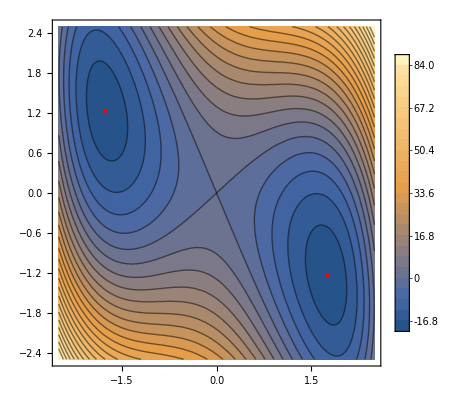

```mathematica
ContourPlot[multivariateFunction[x,y],{x,-5/2,5/2},{y,-5/2,5/2},Contours->25,Epilog->{Red,PointSize[Large],Point[{x,y}/.multivariateMinimaSols]},PlotLegends->Automatic]
```

It’s instructive to think about these using the first and second order Taylor expansions of the function

```mathematica
Simplify[Normal[Series[f[x,y],{x,x0,1},{y,y0,1}]]]/.Derivative[1,1][f][__]->0
```

f[x0,y0]+(y-y0) f^(0,1)[x0,y0]+(x-x0) f^(1,0)[x0,y0]

Which we can equivalently obtain using

```mathematica
With[{du={δx,δy}},
du.Grad[f[x,y],{x,y}]/.{x->x0,y->y0}]
```

δy f^(0,1)[x0,y0]+δx f^(1,0)[x0,y0]

Expressed in this form, the condition for a function to be at a minimum, maximum, or saddle point is given by

where the funky symbol means “for all possible choices of du”

Similarly, to second order we have

```mathematica
Simplify[Normal[Series[f[x,y],{x,x0,2},{y,y0,2}]]]/.{Derivative[2,2][f][__]->0,Derivative[1,2][f][__]->0,Derivative[2,1][f][__]->0}
```

f[x0,y0]+(y-y0) f^(0,1)[x0,y0]+1/2 (y-y0)^2 f^(0,2)[x0,y0]+(x-x0) (f^(1,0)[x0,y0]+(y-y0) f^(1,1)[x0,y0])+1/2 (x-x0)^2 f^(2,0)[x0,y0]

```mathematica
With[{du={δx,δy}},
Expand[1/2 du.hessian[f,{x,y}].du/.{x->x0,y->y0}]]
```

1/2 δy^2 f^(0,2)[x0,y0]+δx δy f^(1,1)[x0,y0]+1/2 δx^2 f^(2,0)[x0,y0]

with the condition

## Thermodynamic Stability

Back to our thermodynamic potentials

Euler’s equation suggests that there are specific values of entropy and volume which minimize the internal energy

Meaning the following form is greater than zero

I.e. the Hessian is positive semi-definite

```mathematica
MatrixForm[
hessian[U,{S,V}]
]
```

(U^(2,0)[S,V] | U^(1,1)[S,V]
U^(1,1)[S,V] | U^(0,2)[S,V])

We can use the fundamental thermodynamic relation to simplify this further by identifying

To obtain

```mathematica
MatrixForm[
internalEnergyHessian={{dtds,dtdv},{dtdv,-dpdv}}
]
```

(dtds | dtdv
dtdv | -dpdv)

```mathematica
Reduce[Thread[Eigenvalues[internalEnergyHessian]>0],
{dpdv,dtds},Reals]
```

dpdv<0&&dtds>-dtdv^2/dpdv

```mathematica
internalEnergyStability=Reduce[Thread[Eigenvalues[internalEnergyHessian]>0],
{dpdv,dtds},Reals]
```

dpdv<0&&dtds>-dtdv^2/dpdv

In-fact, we’ve already encountered the first condition when we talked about the Van der Waals gas, and specified its bulk modulus has to be positive

Note: We used the isothermal bulk modulus, whereas we now derived a condition on the isentropic bulk modulus

## Physical Properties of Crystals

Physical properties or observables are measurable quantities of the state of a physical system.

While certain physical properties, like the mass density of a material, are isotropic, preferred directions in crystals imply that others, such as the stiffness tensor of elastic materials, depend on direction.

Since physical properties represent measurable quantities, they are by definition measured in a particular reference frame.

It stands to reason, that if a set of measurements in a different reference frame represent the same physical property, there must exist  transformation between the two reference frames relating the measured physical quantities.

In this section, we will introduce this relationship.

### Intrinsic “Tensor” Symmetries

Consider a magnetized crystal 

-Graphics-

The work done by the battery is given by:

The first term is related to Joule heating and does not depend on the magnetic field, H_i or magnetic induction, B_i direction

The second term updates our fundamental thermodynamic relation to read:

We can relate the magnetic induction, B, and magnetic field, H, using a constitutive relationship given by

where I is the magnetization intensity

In isotropic materials, we can express the intensity of magnetization to the field strength using

where ψ is the magnetic susceptibility

More generally, the intensity of magnetization need to be parallel to the applied field, giving for anisotropic crystals

Combining these, we obtain the additional work term as

where we’ve introduced the permeability tensor μ_ij=μ_0(δ_ij+ψ_ij)

If we write this out fully we have:

As such we can write:

Differentiating the first expression wrt H_2 and the second wrt H_1 we obtain

However, we know from the equality of mixed partials that these should be identical

Thus we conclude that μ_ij=μ_ji

This is an “intrinsic” tensor symmetry, which states that the permeability tensor is invariant under permutation of the indices i ↔ j

I.e. the rank-2 tensor is symmetric.

There’s a very convenient way to express these in mathematica

```mathematica
MatrixForm[
permeabilityTensor=
With[{symbolName=μ,d=3},
Normal[
SymmetrizedArray[pos_:>Indexed[symbolName,pos],{d,d},{
{Cycles[{{1,2}}],1}}
]]]]
```

(μ11 | μ12 | μ13
μ12 | μ22 | μ23
μ13 | μ23 | μ33)

### Coordinate Transformations (Review)

We can define a transformation between two sets of reference frames

and

where the matrix α_ijrepresents the direction cosines between the two reference frames

-Graphics-

In-fact, you’ve seen this before in the notebook `3.019_L12=Change_of_Basis_Stiffness_Outline.nb` from last semester (which I’ll upload again on canvas)!

We will quickly review some concepts here, and extend the analysis to Thermodynamic stability

#### Einstein Summation Convention

Left-Multiplying a vector with a matrix

Multiplication of Matrices

where

#### Rotating a Rank - 2 Tensor

Consider an “old” (Orange) and a “new” (Blue) coordinate system

Denote the direction cosines matrix mapping a vector from one coordinate system to another

-Graphics-

-Graphics-

is the same vector, but expressed in a different coordinate systems.

For example, suppose the "Blue coordinate system" is rotated by Pi/4 around the z-axis from the Orange (original) one.

```mathematica
orangeVector = {1,3,-1};
blueVector = RotationMatrix[Pi/4,{0,0,1}].orangeVector
```

{-√2,2 √2,-1}

```mathematica
Inverse[RotationMatrix[Pi/4,{0,0,1}]].blueVector
```

{1,3,-1}

Physical property tensors in either coordinate system are given by:

-Graphics-
-Graphics-

These are the same vectors and same rank-2 tensors, but expressed in different coordinate systems.

Suppose now we know a rank-2 physical property tensor in the old (orange) coordinate system
-Graphics-

How do we express the same physical property tensor, but in the blue coordinate system?

Transform the vectors
-Graphics-

Left-multiply by the inverse  
-Graphics-

Note that the inverse of going from blue to orange is going from orange to blue we have:
-Graphics-

This finally gives the relations:
-Graphics-
and
-Graphics-

Example: Rotation of π/2 around [0,0,1]

Rank-2 tensor in “old” coordinate system

```mathematica
MatrixForm[orangeRank2Tensor= Table[Indexed[m,Sort[{i,j}]],{i,3},{j,3}]]
```

(m11 | m12 | m13
m12 | m22 | m23
m13 | m23 | m33)

Transformation from “orange” to “blue”

```mathematica
MatrixForm[orangeToBlue = RotationMatrix[Pi/2,{0,0,1}]]
```

(0 | -1 | 0
1 | 0 | 0
0 | 0 | 1)

The inverse transformation from “blue” to “orange”

```mathematica
MatrixForm[blueToOrange=Simplify[ Inverse[orangeToBlue]]]
```

(0 | 1 | 0
-1 | 0 | 0
0 | 0 | 1)

Note: For symmetry operators such as rotations (which have determinant = 1), the inverse is the same as the transpose.

The Rank-2 tensor in the “new” coordinate system is given by:

```mathematica
MatrixForm[Simplify[orangeToBlue.orangeRank2Tensor.blueToOrange]]
```

(m22 | -m12 | -m23
-m12 | m11 | m13
-m23 | m13 | m33)

### Neumann’s Principle

Neumann’s principle states that:

"The symmetry elements of any physical property of a crystal must include the symmetry elements of the point group of that crystal"

What this means for us, is that if we rotate a tensor using any of the symmetry operations of its point group, the resulting tensors must be identical

This therefore enforces “crystal symmetry” constraints of the form of the tensor

As an example, let’s suppose we are looking at a material which has a four-fold rotation symmetry along the z-axis

```mathematica
MatrixForm[fourFoldRotation=RotationMatrix[π/4,{0,0,1}]]
```

(1/(√2) | -1/(√2) | 0
1/(√2) | 1/(√2) | 0
0 | 0 | 1)

```mathematica
MatrixForm[rotatedPermeabilityTensor=Simplify[fourFoldRotation.permeabilityTensor.Transpose[fourFoldRotation]]
]
```

(1/2 (μ11-2 μ12+μ22) | 1/2 (μ11-μ22) | (μ13-μ23)/(√2)
1/2 (μ11-μ22) | 1/2 (μ11+2 μ12+μ22) | (μ13+μ23)/(√2)
(μ13-μ23)/(√2) | (μ13+μ23)/(√2) | μ33)

Neumann’s principle tells us that these two tensors must be identical

```mathematica
neumannConditions=Thread[Flatten[permeabilityTensor]==Flatten[rotatedPermeabilityTensor]]
```

{μ11==1/2 (μ11-2 μ12+μ22),μ12==1/2 (μ11-μ22),μ13==(μ13-μ23)/(√2),μ12==1/2 (μ11-μ22),μ22==1/2 (μ11+2 μ12+μ22),μ23==(μ13+μ23)/(√2),μ13==(μ13-μ23)/(√2),μ23==(μ13+μ23)/(√2),True}

Which enforces the following constraints

```mathematica
neumannConstraints=First[Solve[neumannConditions,Variables[permeabilityTensor]]]
```

Solve::svars: Equations may not give solutions for all "solve" variables.

{μ12→0,μ13→0,μ22→μ11,μ23→0}

As such, the most general permeability tensor for a material with a four-fold rotation axis around the z-axis (e.g.Tetragonal systems) takes the form

```mathematica
MatrixForm[permeabilityTensor/.neumannConstraints]
```

(μ11 | 0 | 0
0 | μ11 | 0
0 | 0 | μ33)

More generally, Neumann’s principle can be expressed for arbitrary-rank tensors as

where R_ij is any point group operation of the crystal

E.g. for rank-2 tensors we have

and similarly for rank-4 tensors

You will explore this form further in your second assignment!

### Additional Stability Constraints

In addition to the “intrinsic” tensor symmetries and the crystal symmetries introduced by the material’s point group, which determine the independent components in tensors, thermodynamic stability places additional constraints on the values those components can take

As an example, we’ll look at the compliance tensor for an isotropic material

As we saw above, the compliance tensor, s_ijkl, is a rank-4 tensor given by the defining equation:

Since the tensor has both  and  symmetry, we can use a condensed matrix notation instead

where the indices now run from 1-6, with the following scheme:

1 → 11

2 → 22

3 → 33

4 → 23, 32

5 → 13, 31

6 → 12, 21

For an isotropic material, crystal symmetry reduces to matrix to

```mathematica
MatrixForm[isotropicComplianceMatrix={{s11,s12,s12,0,0,0},{s12,s11,s12,0,0,0},{s12,s12,s11,0,0,0},{0,0,0,2 (s11-s12),0,0},{0,0,0,0,2 (s11-s12),0},{0,0,0,0,0,2 (s11-s12)}}]
```

(s11 | s12 | s12 | 0 | 0 | 0
s12 | s11 | s12 | 0 | 0 | 0
s12 | s12 | s11 | 0 | 0 | 0
0 | 0 | 0 | 2 (s11-s12) | 0 | 0
0 | 0 | 0 | 0 | 2 (s11-s12) | 0
0 | 0 | 0 | 0 | 0 | 2 (s11-s12))

Introducing the more common  notation, where E is Young’s Modulus, G is the Rigidity (or Shear) Modulus, and  is Poisson’s ratio, we obtain

```mathematica
MatrixForm[
isotropicComplianceMatrix = Simplify[isotropicComplianceMatrix/.{Indexed[s,{1,1}]-> 1/Ε,Indexed[s,{1,2}]-> -ν/Ε}]]
```

(1/Ε | -ν/Ε | -ν/Ε | 0 | 0 | 0
-ν/Ε | 1/Ε | -ν/Ε | 0 | 0 | 0
-ν/Ε | -ν/Ε | 1/Ε | 0 | 0 | 0
0 | 0 | 0 | (2 (1+ν))/Ε | 0 | 0
0 | 0 | 0 | 0 | (2 (1+ν))/Ε | 0
0 | 0 | 0 | 0 | 0 | (2 (1+ν))/Ε)

The strain energy stored in a crystal is given by

Which must be positive for thermodynamic stability, suggesting  must be positive semi-definite

```mathematica
Reduce[Thread[Eigenvalues[isotropicComplianceMatrix] >= 0],{Ε,ν},Reals]
```

Ε>0&&-1≤ν≤1/2

Which specifies that Young’s Modulus must be positive, and that Poisson’s ratio can only take values between -1 and 1/2

In-fact, a material with a Poisson ratio of 1/2 is incompressible

For cubic materials instead, the compliance tensor is given by

```mathematica
MatrixForm[
cubicComplianceMatrix={{s11,s12,s12,0,0,0},{s12,s11,s12,0,0,0},{s12,s12,s11,0,0,0},{0,0,0,s44,0,0},{0,0,0,0,s44,0},{0,0,0,0,0,s44}}]
```

(s11 | s12 | s12 | 0 | 0 | 0
s12 | s11 | s12 | 0 | 0 | 0
s12 | s12 | s11 | 0 | 0 | 0
0 | 0 | 0 | s44 | 0 | 0
0 | 0 | 0 | 0 | s44 | 0
0 | 0 | 0 | 0 | 0 | s44)

Where the extra independent component is related to  and  with the Zener ratio:

```mathematica
MatrixForm[
cubicComplianceMatrix=cubicComplianceMatrix/.s44->2(s11-s12)/α]
```

(s11 | s12 | s12 | 0 | 0 | 0
s12 | s11 | s12 | 0 | 0 | 0
s12 | s12 | s11 | 0 | 0 | 0
0 | 0 | 0 | (2 (s11-s12))/α | 0 | 0
0 | 0 | 0 | 0 | (2 (s11-s12))/α | 0
0 | 0 | 0 | 0 | 0 | (2 (s11-s12))/α)

```mathematica
Reduce[Thread[Eigenvalues[cubicComplianceMatrix] > 0],{s11,s12,α},Reals]
```

s11>0&&-s11/2<s12<s11&&α>0

Which must be a positive constant according to thermodynamic stability